```mathematica
Clear["Global`*"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
npart=4;
nd=3;
nperm=5;
β0=1;
βN=10;
dβ=1;
npoints=(βN-β0)/dβ+1;
nbeads = 3;
firstbead = 32; 
beadexp = Log[2,firstbead];
dabead=0;
```

```mathematica
For[i=0,i<nbeads,i++,For[j=0,j<npoints,j++,sgndata[j][i]=Import[StringJoin["Fermions/sgnTrace",ToString[npart],"-",ToString[nd],"-",ToString[2^(i+beadexp)],"-",ToString[β0+j dβ],"-1000-1-1-0.txt"],"Table"]]]
```

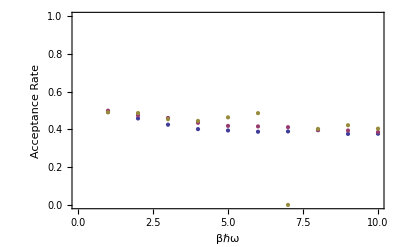

```mathematica
acceptPlot=ListPlot[Table[Table[{i+1,((sgndata[i][j][[3+dabead,1]])/(sgndata[i][j][[3+dabead,1]]+sgndata[i][j][[3+dabead,2]]))},{i,0,βN-1}],{j,0,nbeads-1}],PlotStyle->Thick];
Show[acceptPlot,LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> True,Frame->True,FrameLabel-> {Style["βℏω",Bold],Style["Acceptance Rate",Bold]},PlotRange-> {{0,βN},{0,1}}]
```